```mathematica
M = {{sigma+1, 3}, {-2, sigma-1}}
```

{{1+sigma,3},{-2,-1+sigma}}

```mathematica
M//MatrixForm
```

(1+sigma | 3
-2 | -1+sigma)

```mathematica
Eigenvalues[M]
```

{-ⅈ √5+sigma,ⅈ √5+sigma}

```mathematica
sol[x0_,y0_]:=DSolve[{x'[t] ==((sigma+1)*x[t]+3y[t]) , y'[t] ==(-2*x[t]+(sigma-1)y[t]), x[0]==x0,y[0]==y0},{x,y},{t}]
```

```mathematica
sol[x0,y0]
```

{{x→Function[{t},1/5 ⅇ^(sigma t) (5 x0 Cos[√5 t]+√5 x0 Sin[√5 t]+3 √5 y0 Sin[√5 t])],y→Function[{t},-1/5 ⅇ^(sigma t) (-5 y0 Cos[√5 t]+2 √5 x0 Sin[√5 t]+√5 y0 Sin[√5 t])]}}

```mathematica
{{x->Function[{t},1/5 (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])],y->Function[{t},1/5 (5 v Cos[√5 t]-2 √5 u Sin[√5 t]-√5 v Sin[√5 t])]}}
```

{{x→Function[{t},1/5 (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])],y→Function[{t},1/5 (5 v Cos[√5 t]-2 √5 u Sin[√5 t]-√5 v Sin[√5 t])]}}

```mathematica
x0 = u
y0 = v
```

u

v

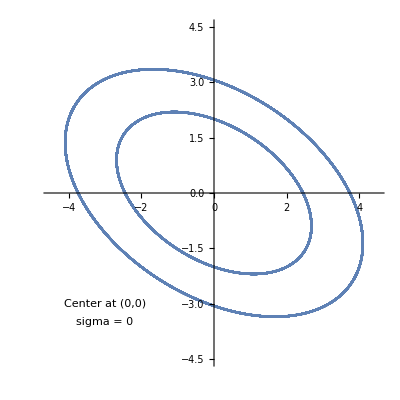

```mathematica
minx=-2;
miny=-2;
maxx=2;
maxy=2;
dist = 10;
inits =Join[Table[ {minx,y},{y,miny,maxy,dist}],Table[ {maxx,y},{y,miny,maxy,dist}],Table[ {x,miny},{x,minx,maxx,dist}],Table[ {x,maxy},{x,minx,maxx, dist}]];
text = Graphics[Text["sigma = 0", {-3,-3.5}]];
text2 = Graphics[Text["Center at (0,0)", {-3, -3}]];
p0 = Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[inits[[i,1]],inits[[i,2]]]],{t,0,50},PlotRange->{{minx-2.5,maxx+2.5},{miny-2.5,maxy+2.5}}],{i,Length[inits]}], text, text2]
```

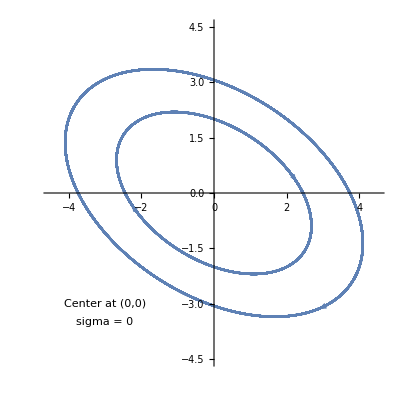

```mathematica
(p0//Normal)/.Line[x_]:>{Arrowheads[{0,0.1,0}],Arrow[x]}
```

```mathematica
sigma = 0
```

0

```mathematica
1/10
```

```mathematica
Norm[x'[t] ==((sigma+1)*x[t]+3y[t]) , y'[t] ==(-2*x[t]+(sigma-1)y[t])]
```

Norm[x'[t]==x[t]+3 y[t],y'[t]==-2 x[t]-y[t]]

```mathematica
u'[t] ==((sigma+1)*u[t]+3u[t])
```

u'[t]==3 u[t]+(1+sigma) u[t]

```mathematica
v[t] ==(-2*v[t]+(sigma-1)v[t])
```

v[t]==-2 v[t]+(-1+sigma) v[t]

```mathematica
Unset[sigma]
Unset[t]
```

```mathematica
sol[x0,y0]
```

{{x→Function[{t},1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])],y→Function[{t},-1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])]}}

```mathematica
u[t_] = sol[x0,y0][[1]]
```

{x→Function[{t},1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])],y→Function[{t},-1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])]}

```mathematica
sigma = -1/10
```

-1/10

```mathematica
t= 0
```

```mathematica
0
Unset[t]
```

0

```mathematica
sigma
```

0

```mathematica
sol[x0,y0]
```

{{x→0},{x→-1/3 √(2-√(4+9 r))},{x→1/3 √(2-√(4+9 r))},{x→-1/3 √(2+√(4+9 r))},{x→1/3 √(2+√(4+9 r))}}[x0,y0]

```mathematica
x/.sol
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.sol

```mathematica
u[t]
```

{x→Function[{t},1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])],y→Function[{t},-1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])]}

```mathematica
{x,y}/.sol
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x,y}/.sol

```mathematica
x[t]/.sol
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x[t]/.sol

```mathematica
x/.(sol[x0,y0])
```

{Function[{t},1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])]}

```mathematica
x
```

x

```mathematica
test = x/.(sol[x0,y0])
```

{Function[{t},1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])]}

```mathematica
test
```

{Function[{t},1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])]}

```mathematica
test2 = test[[1]]
```

Function[{t},1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])]

```mathematica
u[t_] = 1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])
```

1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])

```mathematica
v[t_] = -1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])
```

-1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])

```mathematica
Norm[u[t],v[t]]
```

Norm[1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t]),-1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])]

```mathematica
(u[t])^2
```

1/25 ⅇ^(2 sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])^2

```mathematica
Minimize[(u[t])^2+(v[t])^2,{t}]
```

Minimize[2 (1[t])^2,{t}]

```mathematica
u = 1
v=1
```

1

1